## Cubic Bezier, 2D CSE 477, G. Farin

This notebook illustrates cubic 2D Bezier curves.

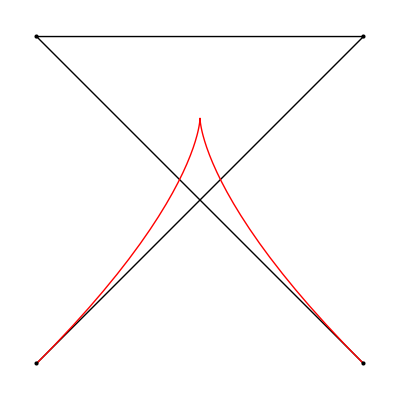

```mathematica
bb={
{{0,0},{-2,0},{0,2},{2,0.0}}, 
{{5,0},{4,1},{2,2},{3,-1}},
{{0,0},{1,1},{0,1},{1,0}},
{{1,1},{1,0},{1,0},{1,0}}
}//N;  (*sample polygons *)

b=bb[[3]]; (* select a control polygon *)

center=Sum[b[[i]],{i,1,4}]/4;
dists=Table[Norm[b[[i]]-center],{i,1,4}];
radius=Max[dists];
 
Do[b[[i]]=b[[i]]-center,{i,1,4}];
(* This moves all points such that their centroid is at the origin. *)

(* The Bernstein polynomials: *)
b30[t_]:=(1-t)^3;
b31[t_]:=3 *(1-t)^2*t ;
b32[t_]:=3*(1-t)*t^2 ;
b33[t_]:=t^3;
(* Alternatively, could have used BernsteinBasis[3,i,t] *)

bez[b_,t_]:=b[[1]]*b30[t]+ b[[2]] *b31[t] +b[[3]] *b32[t] + b[[4]] *b33[t];

plot[b_]:=(
curveplot = ParametricPlot[bez[b,t],{t,0,1},PlotStyle->{Thick, Red}];
polygon=Graphics[Line[b]];
points = Graphics[{PointSize[Large],Point[b]}];
Show[{polygon, curveplot, points},PlotRange->1.3radius]);
plot[b]
```

## Affine Invariance

The next cell illustrates affine invariance. We apply a linear map to the control polygon, and the curve automatically follows.

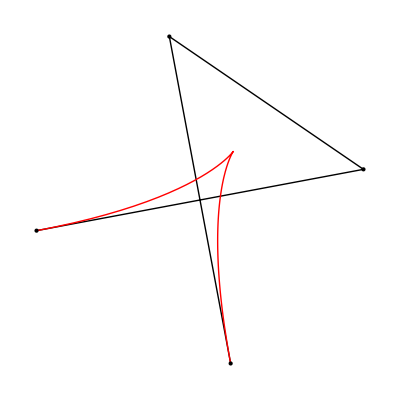

```mathematica
s=-0.6; (* to create a rotation matrix *)
mat = {{Cos[s],-Sin[s]},{Sin[s],Cos[s]}}; 
matb = Table[mat.b[[i]],{i,1,4}];

plot[matb]
```

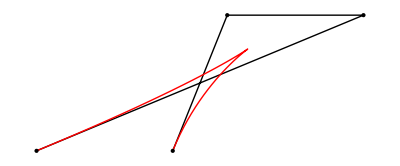

```mathematica
r=1.4; (* to create a shear matrix *)
mat = {{1,r},{0,1}}; 
matb = Table[mat.b[[i]],{i,1,4}];

plot[matb]
```

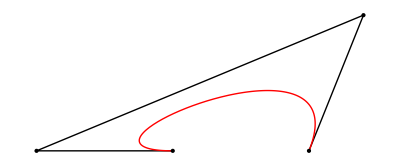

-Graphics-

```mathematica
plot[{{-0.7,-0.5},{-2.7,-0.5},{2.0999999999999996,1.5},{1.3,-0.5}}]
```

## Min-Max Boxes

The next cell illustrates the concept of a minmax-box.

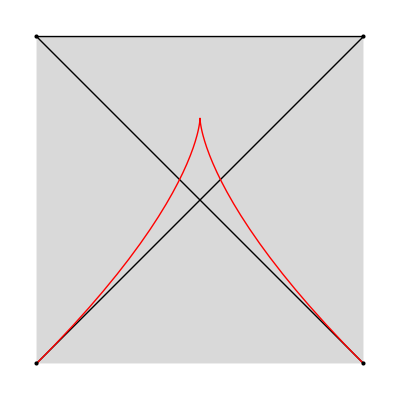

```mathematica
mmbox[poly_] := 
( 
temp = Transpose[poly]; 
{{Min[temp[[1]]], Min[temp[[2]]]}, {Max[temp[[1]]], Max[temp[[2]]]}}
);

boxplot=Graphics[{LightGray,Rectangle[mmbox[b][[1]],mmbox[b][[2]]]}];
Show[boxplot,plot[b]]
```

## Derivatives

The next cell illustrates the concept of a derivative. All second derivative vectors are scaled  for easier display;
Note how second derivatives point “inside” the curve.

```mathematica
der[b_,t_]:=0.33Limit[(bez[b,t+dt]-bez[b,t])/dt,dt->0.0]; (* This is the classical definition tangent =  limit (secant) *)
deriv[b_,t_]:=0.33*(b[[1]]*b30'[t]+ b[[2]] *b31'[t] +b[[3]] *b32'[t] + b[[4]] *b33'[t]);
(* This is an alternative, differentiating the Bernstein polynomials. *)

pointplot[b_,t_]:=Graphics[{PointSize[Large],Green,Point[bez[b,t]]}];
derarrowplot[b_,t_]:=Graphics[{Thick,Green,{Arrowheads[Large],Arrow[{bez[b,t],bez[b,t]+der[b,t]}]}}];

Manipulate[Show[{plot[b],  derarrowplot[b,t], pointplot[b,t]}]
,{t,0,1}]
```

```mathematica
(1-t)'
```

(1-t)'

## Second Derivatives

The next cell illustrates the concept of a second derivative. All second derivative vectors are scaled by 1/3 for easier display;

```mathematica
secderiv[b_,t_]:=0.1*(b[[1]]*b30''[t]+ b[[2]] *b31''[t] +b[[3]] *b32''[t] + b[[4]] *b33''[t]);
(* This is an alternative, twice differentiating the Bernstein polynomials. *)

pointplot[b_,t_]:=Graphics[{PointSize[Large],Green,Point[bez[b,t]]}];
secderarrowplot[b_,t_]:=Graphics[{Thick,Green,{Arrowheads[Large],Arrow[{bez[b,t],bez[b,t]+secderiv[b,t]}]}}];

Manipulate[Show[{plot[b],  secderarrowplot[b,t], pointplot[b,t]}],{t,0,1}]
```